# Equation of the line passing through the two given points

```mathematica
Subscript[x, P_]:=P[[1]];Subscript[y, P_]:=P[[2]];
```

```mathematica
A={2,3};
```

```mathematica
B={0,2};
```

```mathematica
m=(Subscript[y, B]-Subscript[y, A])/(Subscript[x, B]-Subscript[x, A])
```

1/2

```mathematica
y[x_]=m(x-Subscript[x, A])+Subscript[y, A]//Simplify
```

(4+x)/2

```mathematica
PointA=ListPlot[{A,B},PlotRange->{{-5,5},{-5,5}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},AspectRatio->1];
```

```mathematica
Droite=Plot[y[x],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];
```

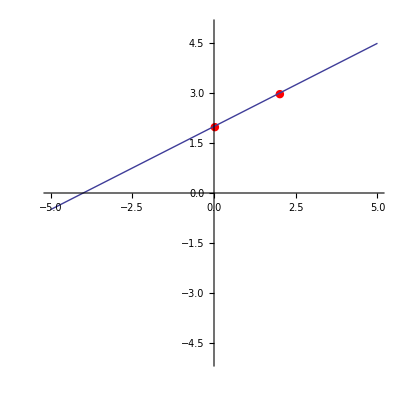

```mathematica
Show[PointA,Droite]
```